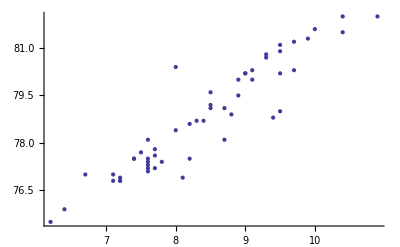

```mathematica
ListPlot[{{7.80000019073486,77.4000015258789},
{8.89999961853027,79.5},
{7.5,77.6999969482422},
{8.30000019073486,78.6999969482422},
{7.69999980926514,77.5999984741211},
{7.69999980926514,77.1999969482422},
{8.69999980926514,79.0999984741211},
{8.69999980926514,78.0999984741211},
{8.39999961853027,78.6999969482422},
{7.59999990463257,77.0999984741211},
{6.40000009536743,75.9000015258789},
{6.19999980926514,75.5},
{9.39999961853027,78.8000030517578},
{7.09999990463257,76.8000030517578},
{8.19999980926514,78.5999984741211},
{7.19999980926514,76.8000030517578},
{7.40000009536743,77.5},
{7.59999990463257,77.1999969482422},
{7.09999990463257,77},
{8.19999980926514,77.5},
{8.10000038146973,76.9000015258789},
{7.19999980926514,76.9000015258789},
{7.19999980926514,76.8000030517578},
{7.59999990463257,77.4000015258789},
{7.59999990463257,77.3000030517578},
{9.69999980926514,80.3000030517578},
{7.40000009536743,77.5},
{7.59999990463257,77.5},
{8,78.4000015258789},
{7.69999980926514,77.8000030517578},
{9.5,79},
{8,80.4000015258789},
{8.80000019073486,78.9000015258789},
{10,81.5999984741211},
{7.59999990463257,78.0999984741211},
{8.5,79.5999984741211},
{8.89999961853027,80},
{9.10000038146973,80},
{8.5,79.1999969482422},
{9.10000038146973,80.3000030517578},
{9.30000019073486,80.8000030517578},
{9,80.1999969482422},
{9.30000019073486,80.6999969482422},
{9.5,80.1999969482422},
{6.69999980926514,77},
{9,80.1999969482422},
{9.5,81.0999984741211},
{9.5,80.9000015258789},
{8.5,79.0999984741211},
{10.8999996185303,82},
{10.3999996185303,82},
{9.69999980926514,81.1999969482422},
{9.89999961853027,81.3000030517578},
{10.3999996185303,81.5}}]
```

```mathematica
t:=Table[{{7.80000019073486,77.4000015258789},
{8.89999961853027,79.5},
{7.5,77.6999969482422},
{8.30000019073486,78.6999969482422},
{7.69999980926514,77.5999984741211},
{7.69999980926514,77.1999969482422},
{8.69999980926514,79.0999984741211},
{8.69999980926514,78.0999984741211},
{8.39999961853027,78.6999969482422},
{7.59999990463257,77.0999984741211},
{6.40000009536743,75.9000015258789},
{6.19999980926514,75.5},
{9.39999961853027,78.8000030517578},
{7.09999990463257,76.8000030517578},
{8.19999980926514,78.5999984741211},
{7.19999980926514,76.8000030517578},
{7.40000009536743,77.5},
{7.59999990463257,77.1999969482422},
{7.09999990463257,77},
{8.19999980926514,77.5},
{8.10000038146973,76.9000015258789},
{7.19999980926514,76.9000015258789},
{7.19999980926514,76.8000030517578},
{7.59999990463257,77.4000015258789},
{7.59999990463257,77.3000030517578},
{9.69999980926514,80.3000030517578},
{7.40000009536743,77.5},
{7.59999990463257,77.5},
{8,78.4000015258789},
{7.69999980926514,77.8000030517578},
{9.5,79},
{8,80.4000015258789},
{8.80000019073486,78.9000015258789},
{10,81.5999984741211},
{7.59999990463257,78.0999984741211},
{8.5,79.5999984741211},
{8.89999961853027,80},
{9.10000038146973,80},
{8.5,79.1999969482422},
{9.10000038146973,80.3000030517578},
{9.30000019073486,80.8000030517578},
{9,80.1999969482422},
{9.30000019073486,80.6999969482422},
{9.5,80.1999969482422},
{6.69999980926514,77},
{9,80.1999969482422},
{9.5,81.0999984741211},
{9.5,80.9000015258789},
{8.5,79.0999984741211},
{10.8999996185303,82},
{10.3999996185303,82},
{9.69999980926514,81.1999969482422},
{9.89999961853027,81.3000030517578},
{10.3999996185303,81.5}}]
```

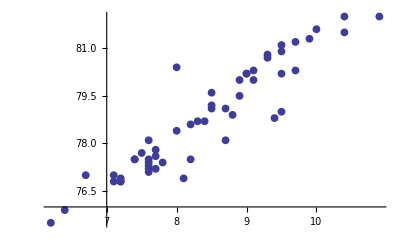

```mathematica
ListPlot[Tooltip[t],PlotStyle->PointSize[0.014]]
```

```mathematica
func:=ListInterpolation[t,InterpolationOrder->1]
```

```mathematica
func[9,9]
```

```mathematica
musculeTable:=Table[{{43.9000015258789,77.4000015258789},{43.4000015258789,79.5},{43.9000015258789,77.6999969482422},{43.5999984741211,78.6999969482422},{44,77.5999984741211},{44.2999992370605,75.9000015258789},{44.4000015258789,75.5},{43.5999984741211,78.8000030517578},{44.0999984741211,76.8000030517578},{43.5999984741211,78.5999984741211},{44.0999984741211,76.8000030517578},{43.9000015258789,77.5},{44,77.1999969482422},{44,77},{43.9000015258789,77.5},{44.0999984741211,76.9000015258789},{44.0999984741211,76.9000015258789},{44.0999984741211,76.8000030517578},{43.9000015258789,77.4000015258789},{44,77.3000030517578},{43.2000007629395,80.3000030517578},{43.9000015258789,77.5},{43.9000015258789,77.5},{43.7000007629395,78.4000015258789},{43.7999992370605,77.8000030517578},{43.5,79},{43.2000007629395,80.4000015258789},{43.5999984741211,78.9000015258789},{42.9000015258789,81.5999984741211},{43.7999992370605,78.0999984741211},{43.4000015258789,79.5999984741211},{43.2999992370605,80},{43.0999984741211,80},{43.5,79.1999969482422},{43.2000007629395,80.3000030517578},{43.0999984741211,80.8000030517578},{43.2000007629395,80.1999969482422},{43.0999984741211,80.6999969482422},{43.2000007629395,80.1999969482422},{44.0999984741211,77},{43.2000007629395,80.1999969482422},{43,81.0999984741211},{43.0999984741211,80.9000015258789},{42.5,79.0999984741211},{42.7999992370605,82},{42.7999992370605,82},{43,81.1999969482422},{43,81.3000030517578},{44,77.1999969482422},{43.5,79.0999984741211},{43.7999992370605,78.0999984741211},{43.5999984741211,78.6999969482422},{44,77.0999984741211}}]
```

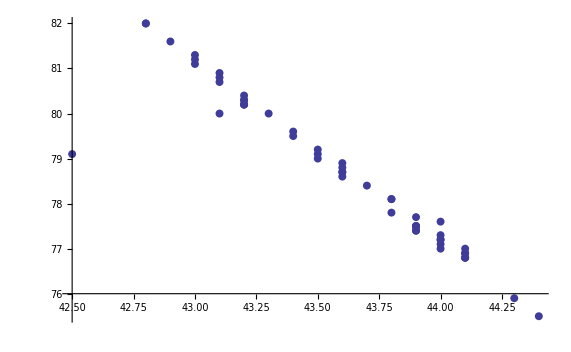

```mathematica
ListPlot[Tooltip[musculeTable],PlotStyle->PointSize[0.01]]
```